```mathematica
Clear[W,M,f,gtable, v,y, x, w12, w13, w23, w34, w21]
```

### Создание графа вычислений https://www.wolframcloud.com/obj/gurgutan/Published/4.2.nb

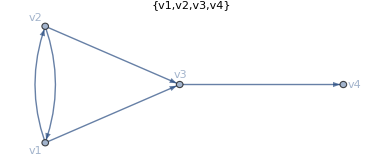
{(0 | 1 | 1 | 0
1 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0),-Graphics-}

```mathematica
v={v1,v2,v3,v4};
M={{0,1,1,0},{1,0,1,0},{0,0,0,1},{0,0,0,0}};
{MatrixForm[M],AdjacencyGraph[M, VertexLabels->Table[i->v[[i]],{i,1,4}] ,PlotLabel->v, GraphLayout->"SpringElectricalEmbedding"]}
```

```mathematica
W={{0,w12,w13,0},{w21,0,w23,0},{0,0,0,w34},{0,0,0,0}};
MatrixForm[W]
```

(0 | w12 | w13 | 0
w21 | 0 | w23 | 0
0 | 0 | 0 | w34
0 | 0 | 0 | 0)

## Получение значений в вершинах графа после 1-й итерации вычислений

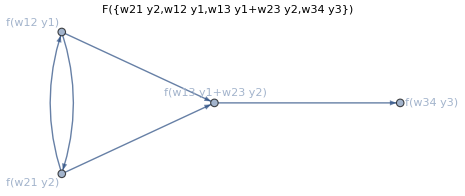
{{w21 y2,w12 y1,w13 y1+w23 y2,w34 y3},{y1,y2,y3,y4},-Graphics-}

```mathematica
y={y1,y2,y3, y4};
x=y.(M*W);
(*  g(y)=f(y.M*W)=f(y.(M*W))=f(y.W')); g:=f(x.W')       *)
gtable = Table[i->f[x[[i]]],{i,1,Length[x]}] ;(* метки вершин в виде функций*)
{x,y,AdjacencyGraph[M, VertexLabels-> gtable,PlotLabel->F[x], GraphLayout->"SpringElectricalEmbedding"]}
```

## После определения функций f мы можем вычислить значения в вершинах графа

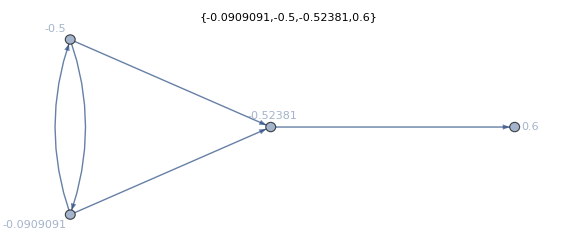

```mathematica
f[x_]:=x/(1+Abs[x]);
y={1,-0.1,1.5,0.5};
w12=-1;w13=-1;w23=1;w34=1;w21=1;
x=y.(M*W);
y=f[x];
AdjacencyGraph[M, VertexLabels->Table[i->y[[i]],{i,1,4}] ,PlotLabel->f[x], GraphLayout->"SpringElectricalEmbedding"]
```

## Выполенение нескольких итераций вычислений

{{1.03948,1.03948,1.15198,1.23106},{1.80838,1.80838,1.,1.94279},{2.71374,2.71374,1.,1.76159},{3.69,3.69,1.,1.76159},{4.6854,4.6854,1.,1.76159},{5.6846,5.6846,1.,1.76159},{6.68447,6.68447,1.,1.76159},{7.68445,7.68445,1.,1.76159},{8.68444,8.68444,1.,1.76159},{9.68444,9.68444,1.,1.76159}}

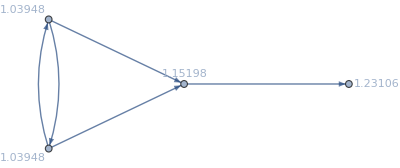
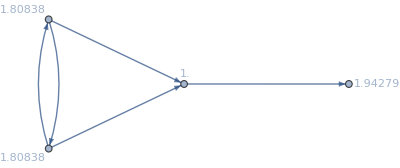
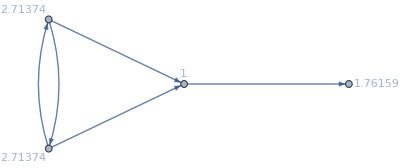
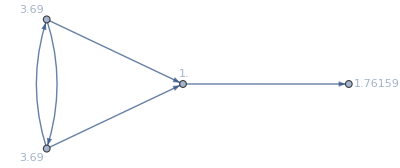
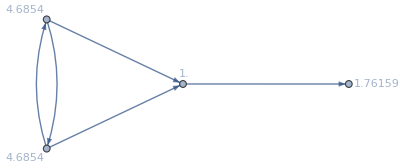
1 | -Graphics-
2 | -Graphics-
3 | -Graphics-
4 | -Graphics-
5 | -Graphics-

```mathematica
f[x_]:=x Tanh[x]+1;
Y=RecurrenceTable[{z[n]==f[z[n-1].(M*W)],z[0]=={0.2,-0.2,0.5,0.2}},z,{n,1,10}]
TableForm[Table[{n,AdjacencyGraph[M, VertexLabels->Table[i->Y[[n,i]],{i,1,4}] , GraphLayout->"SpringElectricalEmbedding"]}, {n,1,5}]]
```